```mathematica
ds=b(s+i)-β0 v/(h+v) s i-μ s
di=β0 v/(h+v) s i-(μ+v) i
dv=W (D[β0 v/(h+v) s-(μ+v),v])//Simplify
```

b (i+s)-(i s v β0)/(h+v)-s μ

(i s v β0)/(h+v)-i (v+μ)

W (-1+(h s β0)/(h+v)^2)

```mathematica
equil=Solve[{ds==0,di==0,dv==0},{s,i,v}][[2]]//Simplify
```

{s→(√h+√μ)^2/β0,i→-((√h+√μ)^2 (-b+μ))/(β0 (-b+√h √μ+μ)),v→√h √μ}

```mathematica
(* here is the TEA when the population is away from equilibrium *)
Solve[-1+(h s β0)/(h+v)^2==0,v][[2]]
```

{v→-h+√h √s √β0}

```mathematica
(* to get a feasible equilibrium, require that -b+√h √μ+μ > 0 *) 
(* which is equivalent to h > (b-μ)^2/μ *)
```

```mathematica
Solve[-b+√h √μ+μ ==0,h]//Simplify
```

{{h→(b-μ)^2/μ}}

```mathematica
(* equilibrium prevalence *)
equil[[2,2]]/(equil[[1,2]]+equil[[2,2]])//Simplify
```

(b-μ)/(√h √μ)

```mathematica
equil[[1,2]]+equil[[2,2]]//Simplify
```

(√h (√h+√μ)^2 √μ)/(β0 (-b+√h √μ+μ))

```mathematica
ds2=b (i+s)-β s i-s μ
di2=β s i-(μ+v) i
```

b (i+s)-i s β-s μ

i s β-i (v+μ)

```mathematica
(* Non-dimensionalize the system *)
Expand[that/shat (ds2/.{s->S shat,i->Ι ihat})]/.that->1/b/.ihat->b/β/.shat->b/β
Expand[that/ihat (di2/.{s->S shat,i->Ι ihat})]/.that->1/b/.ihat->b/β/.shat->b/β
```

S+Ι-S Ι-(S μ)/b

S Ι-(v Ι)/b-(Ι μ)/b

```mathematica
ds2=S+Ι-S Ι-m S
di2=S Ι-v Ι-m Ι
```

S-m S+Ι-S Ι

-m Ι+S Ι-v Ι

```mathematica
(* Does the non-evolutionary system have any tendency to oscillate? *)
equil2=Simplify[Solve[{ds2==0,di2==0},{S,Ι}]]
Simplify[Eigenvalues[D[{ds2,di2},{{S,Ι}}]]]
```

{{S→0,Ι→0},{S→m+v,Ι→-((-1+m) (m+v))/(-1+m+v)}}

{1/2 (1-2 m+S-v-Ι-√(S^2+v^2-2 v (-1+Ι)+(1+Ι)^2-2 S (1+v+Ι))),1/2 (1-2 m+S-v-Ι+√(S^2+v^2-2 v (-1+Ι)+(1+Ι)^2-2 S (1+v+Ι)))}

```mathematica
(* want to make this positive, or at least a small imaginary part *)
Expand[(S^2+v^2-2 v (-1+Ι)+(1+Ι)^2-2 S (1+v+Ι)/.{S->m+v})]==
Expand[(1+Ι-m)^2-4 v Ι]
```

```mathematica
True
```

```mathematica
(* What you can see from this is that the lone controls come through μ and b (since ν is evolving *)
oscill=((1-m)(1+(m+v)/(-1+m+v)))^2-4 v ((1-m) (m+v))/(-1+m+v)/.{v->ν/b,m->μ/b}
```

-(4 (1-μ/b) ν (μ/b+ν/b))/(b (-1+μ/b+ν/b))+(1-μ/b)^2 (1+(μ/b+ν/b)/(-1+μ/b+ν/b))^2

```mathematica
params={b->20,μ->15,β0->0.1,h->5,W->0.01};
(* at the ESS ν *)
N[oscill/.ν->√h √μ/.params]
```

0.683013

```mathematica
(* Here you go: no tendency to oscillate here *)
```

```mathematica
params={b->20,μ->15,β0->0.1,h->5,W->0.01};
(* feasible equilibrium *)
equil/.params
(* Stability of feasible equilibria *)
Eigenvalues[D[{ds,di,dv},{{s,i,v}}]/.equil/.params]
```

{s→373.205,i→509.808,v→5 √3}

{-21.9239,-5.39662,-0.00146393}

```mathematica
params={b->15,μ->10,β0->0.1,h->5,W->0.01};
(* feasible equilibrium *)
equil/.params
(* Stability of feasible equilibria *)
Eigenvalues[D[{ds,di,dv},{{s,i,v}}]/.equil/.params]
```

{s→291.421,i→703.553,v→5 √2}

{-33.678,-2.53517,-0.00165639}

```mathematica
Solve[{ds==0,di==0},{s,i}]
```

{{s→0,i→0},{s→((h+v) (v+μ))/(v β0),i→((h+v) (b-μ) (v+μ))/(v β0 (-b+v+μ))}}

```mathematica
params={b->2,μ->1.7,β0->0.12,h->0.1,W->0.01};
(* feasible equilibrium *)
equil/.params
(* Stability of feasible equilibria *)
Eigenvalues[D[{ds,di,dv},{{s,i,v}}]/.equil/.params]
```

{s→21.8718,i→58.4233,v→0.412311}

{-5.21567,-0.1289,-0.0367971}

```mathematica
{s'[t]==((b (s[t]+i[t])-β0 (1+β1 Cos[ω t]) s[t] i[t]-m s[t]+γ i[t])/.{b->1,β0->0.5,β1->2,ω->0.1,γ->0.01}),
i'[t]==((β0 (1+β1 Cos[ω t]) s[t] i[t]-(m+v+γ) i[t])/.{b->1,β0->0.5,β1->2,ω->0.1,γ->0.01,v->1}),
s[0]==100,i[0]==1}
```

{s'[t]==1.01 i[t]+s[t]-m s[t]-0.5 (1+2 Cos[0.1 t]) i[t] s[t],i'[t]==-(1.01+m) i[t]+0.5 (1+2 Cos[0.1 t]) i[t] s[t],s[0]==100,i[0]==1}

```mathematica
out=NDSolve[{s'[t]==((b (s[t]+i[t])-β0 (1+β1 Cos[ω t]) s[t] i[t]-m s[t]+γ i[t])/.{b->1,β0->0.05,β1->0.2,ω->2,γ->0.01,m->0.6}),
i'[t]==((β0 (1+β1 Cos[ω t]) s[t] i[t]-(m+v+γ) i[t])/.{b->1,β0->0.05,β1->0.2,ω->2,γ->0.01,v->1,m->0.6}),
s[0]==100,i[0]==1},{s,i},{t,0,100}]
out1=NDSolve[{s'[t]==((b (s[t]+i[t])-β0 (1+β1 Cos[ω t]) s[t] i[t]-m s[t]+γ i[t])/.{b->1,β0->0.05,β1->0.2,ω->1,γ->0.01,m->0.6}),
i'[t]==((β0 (1+β1 Cos[ω t]) s[t] i[t]-(m+v+γ) i[t])/.{b->1,β0->0.05,β1->0.2,ω->1,γ->0.01,v->1,m->0.6}),
s[0]==100,i[0]==1},{s,i},{t,0,100}]
```

{{s→InterpolatingFunction[{{0., 100.}}, <>],i→InterpolatingFunction[{{0., 100.}}, <>]}}

{{s→InterpolatingFunction[{{0., 100.}}, <>],i→InterpolatingFunction[{{0., 100.}}, <>]}}

The key issue here is that the frequency of oscillations must be very high to represent diel fluctuations - e.g., diel fluctuations occur on the scale of a day, but transmission will probably measured on a much slower timescale. Thus, the prevalence should not fluctuate at a similar frequency as the high frequency diel oscillations.

Assuming t is measured in days, the period of oscillations actually fixed, since the period should be equal to 1 day (plus or minus a little). Thus, if the circadian rhythm is given by a cosine wave, cos(ω t), then the period is 2π/ω.

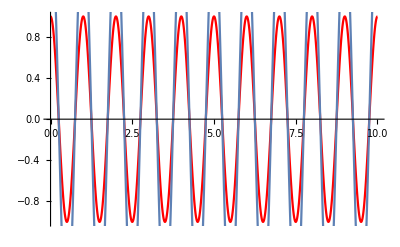

```mathematica
Show[Plot[Cos[ω t]/.ω->2 π,{t,0,10},PlotStyle->{Red}],Plot[2 Cos[ω t]/.ω->2 π,{t,0,10}]]
```

What if you shift?

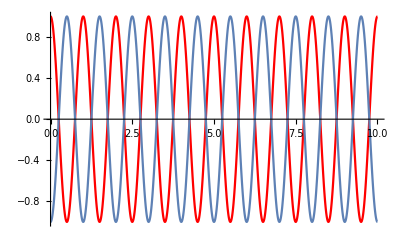

```mathematica
Show[Plot[Cos[ω t]/.ω->2 π,{t,0,10},PlotStyle->{Red}],Plot[Cos[ω t-π]/.ω->2 π,{t,0,10}]]
```

```mathematica
params1={b->0.4,β0->0.04,β1->1,ω->2 π,γ->1/5,v->1,m->1/40};
out1=NDSolve[{s'[t]==((b (s[t]+i[t])-β0 (1+β1 Cos[ω t]) s[t] i[t]-m s[t]+γ i[t])/.params1),
i'[t]==((β0 (1+β1 Cos[ω t]) s[t] i[t]-(m+v+γ) i[t])/.params1),
s[0]==100,i[0]==1},{s,i},{t,0,100}];
params2={b->0.4,β0->0.04,β1->0.01,ω->2 π,γ->1/5,v->1,m->1/40};
out2=NDSolve[{s'[t]==((b (s[t]+i[t])-β0 (1+β1 Cos[ω t]) s[t] i[t]-m s[t]+γ i[t])/.params2),
i'[t]==((β0 (1+β1 Cos[ω t]) s[t] i[t]-(m+v+γ) i[t])/.params2),
s[0]==100,i[0]==1},{s,i},{t,0,100}];
```

Varying the magnitude of oscillations doesn’t have a big effect, as it turns out.

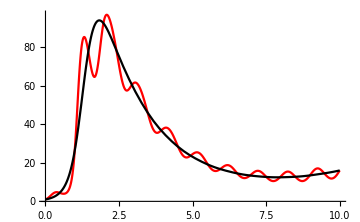

```mathematica
Show[Plot[i[t]/.out1,{t,0,10},PlotRange->All,PlotStyle->{Red}],
Plot[i[t]/.out2,{t,0,10},PlotRange->All,PlotStyle->{Black}]]
```

What if you shift so the epidemic happens during a low transmission period?

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

Here’s a crazy case where introducing a highly virulent pathogen at a moment of high infection risk (red) versus low infection risk (black) has consequences that play out over the next several weeks!

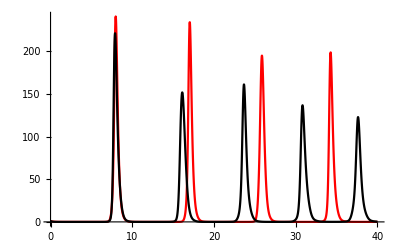

```mathematica
params3={b->0.3,β0->0.02,β1->0.1,ω->2 π,γ->1/5,v->6,m->1/40};
out3=NDSolve[{s'[t]==((b (s[t]+i[t])-β0 (1+β1 Cos[ω t]) s[t] i[t]-m s[t]+γ i[t])/.params3),
i'[t]==((β0 (1+β1 Cos[ω t]) s[t] i[t]-(m+v+γ) i[t])/.params3),
s[0]==100,i[0]==1},{s,i},{t,0,100},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},AccuracyGoal->Infinity, PrecisionGoal->12];
out4=NDSolve[{s'[t]==((b (s[t]+i[t])-β0 (1+β1 Cos[ω t-π]) s[t] i[t]-m s[t]+γ i[t])/.params3),
i'[t]==((β0 (1+β1 Cos[ω t-π]) s[t] i[t]-(m+v+γ) i[t])/.params3),
s[0]==100,i[0]==1},{s,i},{t,0,100},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},AccuracyGoal->Infinity, PrecisionGoal->12];
Show[Plot[i[t]/.out3,{t,0,40},PlotRange->All,PlotStyle->{Red}],
Plot[i[t]/.out4,{t,0,40},PlotRange->All,PlotStyle->{Black}]]
```

Same results, but looking at prevalence:

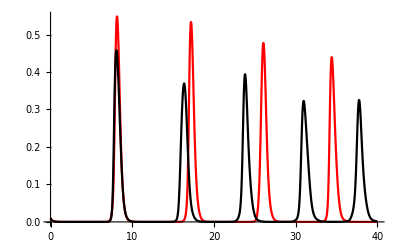

```mathematica
Show[Plot[i[t]/(i[t]+s[t])/.out3,{t,0,40},PlotRange->All,PlotStyle->{Red}],
Plot[i[t]/(i[t]+s[t])/.out4,{t,0,40},PlotRange->All,PlotStyle->{Black}]]
```

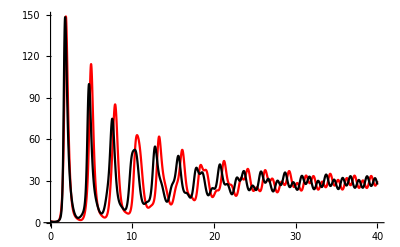

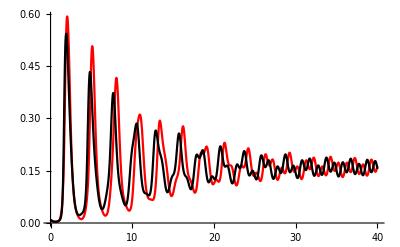

```mathematica
params3={b->1,β0->0.04,β1->0.1,ω->2 π,γ->1/10,v->6,m->1/20};
out3=NDSolve[{s'[t]==((b (s[t]+i[t])-β0 (1+β1 Cos[ω t]) s[t] i[t]-m s[t]+γ i[t])/.params3),
i'[t]==((β0 (1+β1 Cos[ω t]) s[t] i[t]-(m+v+γ) i[t])/.params3),
s[0]==100,i[0]==1},{s,i},{t,0,100},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},AccuracyGoal->Infinity, PrecisionGoal->12];
out4=NDSolve[{s'[t]==((b (s[t]+i[t])-β0 (1+β1 Cos[ω t-π]) s[t] i[t]-m s[t]+γ i[t])/.params3),
i'[t]==((β0 (1+β1 Cos[ω t-π]) s[t] i[t]-(m+v+γ) i[t])/.params3),
s[0]==100,i[0]==1},{s,i},{t,0,100},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False},AccuracyGoal->Infinity, PrecisionGoal->12];
Show[Plot[i[t]/.out3,{t,0,40},PlotRange->All,PlotStyle->{Red}],
Plot[i[t]/.out4,{t,0,40},PlotRange->All,PlotStyle->{Black}]]
Show[Plot[i[t]/(i[t]+s[t])/.out3,{t,0,40},PlotRange->All,PlotStyle->{Red}],
Plot[i[t]/(i[t]+s[t])/.out4,{t,0,40},PlotRange->All,PlotStyle->{Black}]]
```

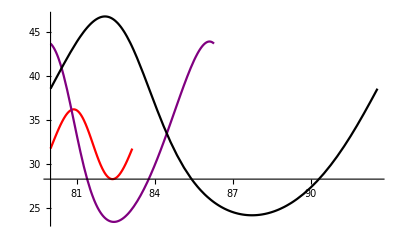

```mathematica
Show[Plot[s[t]/.out1,{t,80,83.1416},PlotStyle->Red],
Plot[s[t]/.out2,{t,80,86.2832},PlotStyle->Purple],Plot[s[t]/.out3,{t,80,92.56637},PlotStyle->Black],PlotRange->All]
```

```mathematica
Mean[Table[(s[t]/.out1)[[1]],{t,80,83.1416,0.001}]]
Mean[Table[(s[t]/.out2)[[1]],{t,80,86.2832,0.001}]]
Mean[Table[(s[t]/.out3)[[1]],{t,80,92.56637,0.001}]]
```

32.2366

32.7161

33.2868

```mathematica
DSolve[{S'[t]==-β S[t] Z[t],i'[t]==β S[t] Z[t],Z'[t]==-β n Z[t],S[0]==0.99,i[0]==0.01,Z[0]==150},{S,i,Z},t]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 150/n-Log[ⅇ^(C[1]/n)] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Z→Function[{t},150. ⅇ^(-n t β)],i→Function[{t},-0.99 ⅇ^(-150./n) (-1.0101 ⅇ^(150./n)+1. ⅇ^((150. ⅇ^(-n t β))/n))],S→Function[{t},0.99 ⅇ^(-150./n+(150. ⅇ^(-n t β))/n)]}}

```mathematica
DSolve[{S'[t]==-β S[t] Z[t],Z'[t]==-β S[t] Z[t],S[0]==1,Z[0]==100},{S,Z},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Z→Function[{t},(9900 ⅇ^(99 t β))/(-1+100 ⅇ^(99 t β))],S→Function[{t},99/(-1+100 ⅇ^(99 t β))]}}